```mathematica
fmass={0.5109,0,105.658,0,1776.86,0,2.2,4.7,1270,96,173210,4180}*1*10^-3;
mv={80.385,91.1876};
mh=125.09;
thetaW=ArcSin[√0.23120];
sw2=Sin[thetaW]^2;

ga={-0.5,0.5,-0.5,0.5,-0.5,0.5,0.5,-0.5,0.5,-0.5,0.5,-0.5};
gv={0.5,-0.5+2*sw2,0.5,-0.5+2*sw2,0.5,-0.5+2*sw2,0.5-4*sw2/3.,-0.5+2*sw2/3.,0.5-4*sw2/3.,-0.5+2*sw2/3.,0.5-4*sw2/3.,-0.5+2*sw2/3.};
Nc={1,1,1,1,1,1,3,3,3,3,3,3};
(*gs=1.214 ;*)
v=246;
alphas=0.1182 ;
gs=√(4π*alphas);
GF=1.166*10^-5;
(*g2=8*mv[[1]]^2/(√2)*GF;*)
ge=0.302822;
gw=0.6295;
gz=0.7180;
t12=ArcSin[√0.297];
t23=ArcSin[√0.437];
t13=ArcSin[√0.0214];
s12=Sin[t12];
s23=Sin[t23];
s13=Sin[t13];
c12=Cos[t12];
c23=Cos[t23];
c13=Cos[t13];
PMNS=Transpose[{{c12*c13,-s12*c23-c12*s23*s13,s12*s23-c12*c23*s13},{s12*c13,c12*c23-s12*s23*s13,-c12*s23-s12*c23*s13},{s13,s23*c13,c23*c13}}];
CKM=Transpose[{{0.97434,0.22492,0.00875},{0.22506,0.97351,0.0403},{0.00357,0.0411,0.99915}}];
Mp=2.435*10^18;
GeV2sec=6.58*10^-25;
kappa=1./Mp ;
DMMass1=Table[i,{i,1,1000,1}];
DMMass2=Table[i,{i,10^3,10^6,10^3}];
DMMass=Catenate[{DMMass1,DMMass2}];
(*DMMass=Table[i,{i,10^3,10^6,10^4}];*)
cota1=4*10^16;
cota2=1*10^23;
Gamma1=Table[0,{i,1,Length[DMMass]}];
Gamma2=Table[0,{i,1,Length[DMMass]}];
Gamma3=Table[0,{i,1,Length[DMMass]}];
Gamma41=Table[0,{i,1,Length[DMMass]}];
Gamma51=Table[0,{i,1,Length[DMMass]}];
Gamma61=Table[0,{i,1,Length[DMMass]}];
Gamma71=Table[0,{i,1,Length[DMMass]}];
Gamma81=Table[0,{i,1,Length[DMMass]}];
Gamma91=Table[0,{i,1,Length[DMMass]}];

Gamma42=Table[0,{i,1,Length[DMMass]}];
Gamma52=Table[0,{i,1,Length[DMMass]}];
Gamma62=Table[0,{i,1,Length[DMMass]}];
Gamma72=Table[0,{i,1,Length[DMMass]}];
Gamma82=Table[0,{i,1,Length[DMMass]}];
Gamma92=Table[0,{i,1,Length[DMMass]}];
```

```mathematica
xh[m_]:=mh^2/m^2
xw[m_]:=mv[[1]]^2/m^2
xz[m_]:=mv[[2]]^2/m^2
xf[m_]:=fmass^2/m^2
λ[x_,y_,z_]:=(1-2*(x+y)/z+(x-y)^2/z^2)^(1/2)
p12[s_,m1_,m2_]:=(s-m1^2-m2^2)/2
p13[s_,θ3_,m_,m1_,m2_,m3_]:=1/4(((m^2-s-m3^2)(s+m1^2-m2^2))/s+m^2*λ[m1^2,m2^2,s]*λ[s,m3^2,m^2]*Cos[θ3])
p23[s_,θ12_,m_,m1_,m2_,m3_]:=1/4(((m^2-s-m3^2)(s+m2^2-m1^2))/s-m^2*λ[m1^2,m2^2,s]*λ[s,m3^2,m^2]*Cos[θ12])
Φ[s_,m_,m1_,m2_,m3_]:=(2π)^2/(8^2(2π)^5)λ[m1^2,m2^2,s]*λ[s,m3^2,m^2]
dqqg[s_,m_,m1_,m2_,m3_,ξ_]:=4*9(ξ^2 Mp^2 kappa^4)/(2m)8*gs^2*(p12[s,m1,m2]+2 m1^2)*Φ[s,m,m1,m2,m3]
dffxw[s_,θ12_,θ3_,m_,m1_,m2_,m3_,ξ_]:=9(ξ^2 Mp^2 kappa^4)/(2m)gw^2*(p12[s,m1,m2]+2/m3^2 p13[s,θ3,m,m1,m2,m3]*p23[s,θ12,m,m1,m2,m3])*Φ[s,m,m1,m2,m3]
gp[i_]:=ga[[i]]^2+gv[[i]]^2
gm[i_]:=gv[[i]]^2-ga[[i]]^2
dffxz[s_,θ12_,θ3_,m_,m1_,m2_,m3_,i_,ξ_]:=9*Nc[[i]]*(ξ^2 Mp^2 kappa^4)/(2m)*4/m3^2 gz^2(3*gm[i]*m1*m2*m3^2+gp[i]*m3^2 p12[s,m1,m2]+2p13[s,θ3,m,m1,m2,m3]*p23[s,θ12,m,m1,m2,m3])*Φ[s,m,m1,m2,m3]
Φ2[s12_,s34_,m_,m1_,m2_,m3_,m4_]:=(2π)^3/(8^3(2π)^8)λ[s12,s34,m^2]λ[m1^2,m2^2,s12]λ[m3^2,m4^2,s34]
dhhww[s12_,s34_,m_,m1_,m2_,m3_,m4_,ξ_]:=16(ξ^2 Mp^2 kappa^4)/(2m*v^4)(2*mv[[1]]^4+((s34-2 mv[[1]]^2)/2)^2)*Φ2[s12,s34,m,m1,m2,m3,m4]
dhhzz[s12_,s34_,m_,m1_,m2_,m3_,m4_,ξ_]:=16(ξ^2 Mp^2 kappa^4)/(2m*v^4)(2*mv[[2]]^4+((s34-2 mv[[2]]^2)/2)^2)*Φ2[s12,s34,m,m1,m2,m3,m4]
```

```mathematica
hh[m_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(32π)m^3(1+2*xh[m])^2(1-4*xh[m])^(1/2)
zz[m_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(32π)m^3(1-4*xz[m]+12*xz[m]^2)*(1-4*xz[m])^(1/2)
ww[m_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(16π)m^3(1-4*xw[m]+12*xw[m]^2)*(1-4*xw[m])^(1/2)
ffx[m_,m1_,i_,ξ_]:=25*Nc[[i]](ξ^2 Mp^2 kappa^4)/(8π)m*m1^2(1-4*m1^2/m^2)^(3/2)
qqg[m_,m1_,m2_,m3_,ξ_]:=NIntegrate[dqqg[s,m,m1,m2,m3,ξ],{s,(m1+m2)^2,(m-m3)^2}]
ffxw[m_,m1_,m2_,m3_,ξ_]:=NIntegrate[dffxw[s,θ12,θ3,m,m1,m2,m3,ξ],{s,(m1+m2)^2,(m-m3)^2},{θ12,0,π},{θ3,0,π}]
ffxz[m_,m1_,m2_,m3_,i_,ξ_]:=NIntegrate[dffxz[s,θ12,θ3,m,m1,m2,m3,i,ξ],{s,(m1+m2)^2,(m-m3)^2},{θ12,0,π},{θ3,0,π}]
hhww[m_,m1_,m2_,m3_,m4_,ξ_]:=NIntegrate[dhhww[s12,s34,m,m1,m2,m3,m4,ξ],{s12,(m1+m2)^2,(m-m3-m4)^2},{s34,(m3+m4)^2,(m-√s12)^2},AccuracyGoal->20]
hhzz[m_,m1_,m2_,m3_,m4_,ξ_]:=NIntegrate[dhhzz[s12,s34,m,m1,m2,m3,m4,ξ],{s12,(m1+m2)^2,(m-m3-m4)^2},{s34,(m3+m4)^2,(m-√s12)^2},AccuracyGoal->20]
```

```mathematica
ffx2[m_,m1_,i_,ξ_]:=Nc[[i]](ξ^2 Mp^2 kappa^4)/(8π)m*m1^2(1-4*m1^2/m^2)^(3/2)
qqg2[m_,ξ_]:=(alphas*ξ^2 Mp^2 kappa^4)/(4 π^2)m^3
ffxw2[m_,ξ_]:=3/(√32)GF*(ξ^2 Mp^2 kappa^4)/(4π)^3 m^5
ffxz2[m_,i_,ξ_]:=3/(√8)GF*(ga[[i]]^2+gv[[i]]^2)(ξ^2 Mp^2 kappa^4)/(4π)^3 m^5
hhww2[m_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(15(8π)^5 v^4)m^7
hhzz2[m_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(30(8π)^5 v^4)m^7
```

```mathematica
ξ=1;
For[i=1,i<=Length[DMMass],i++,{
m=DMMass[[i]];

If[m>2*mh,Gamma1[[i]]=hh[m,ξ]];

If[m>2*mv[[2]],Gamma2[[i]]=zz[m,ξ]];

If[m>2*mv[[1]],Gamma3[[i]]=ww[m,ξ]];

For[ii=1,ii<13,ii++,{
If[m>2*fmass[[ii]],{
Gamma41[[i]]+=ffx[m,fmass[[ii]],ii,ξ];
Gamma42[[i]]+=ffx2[m,fmass[[ii]],ii,ξ]}]}];

For[ii=7,ii<13,ii++,{
	If[m>2*fmass[[ii]],{
Gamma51[[i]]+=qqg[m,fmass[[ii]],0,fmass[[ii]],ξ];
Gamma52[[i]]+=qqg2[m,ξ]}]}];

For[ii=0,ii<3,ii++,{
For[jj=0, jj<3, jj++,{
	If[m>fmass[[2*ii+7]]+fmass[[2*jj+8]]+mv[[1]],{
Gamma61[[i]]+=3*ffxw[m,fmass[[2*ii+7]],fmass[[2*jj+8]],mv[[1]],ξ]*(CKM[[ii+1]][[jj+1]])^2;
Gamma62[[i]]+=3*ffxw2[m,ξ]*(CKM[[ii+1]][[jj+1]])^2}]}];}]

For[ii=0,ii<3,ii++,{
For[jj=0, jj<3, jj++,{
	If[m>fmass[[2*ii+1]]+fmass[[2*jj+2]]+mv[[1]],{
Gamma61[[i]]+=ffxw[m,fmass[[2*ii+1]],fmass[[2*jj+2]],mv[[1]],ξ]*(PMNS[[ii+1]][[jj+1]])^2;
Gamma62[[i]]+=ffxw2[m,ξ]*(PMNS[[ii+1]][[jj+1]])^2}]}];}]

For[ii=1,ii<13,ii++,{
	If[m>2*fmass[[ii]]+mv[[2]],{
Gamma71[[i]]+=ffxz[m,fmass[[ii]],fmass[[ii]],mv[[2]],ii,ξ];
Gamma72[[i]]+=ffxz2[m,ii,ξ]}]}];

If[m>2*mh+2*mv[[1]],{
Gamma81[[i]]=hhww[m,mh,mh,mv[[1]],mv[[1]],ξ];
Gamma82[[i]]=hhww2[m,ξ]}];

If[m>2*mh+2*mv[[2]],{
Gamma91[[i]]=hhzz[m,mh,mh,mv[[2]],mv[[2]],ξ];
Gamma92[[i]]=hhzz2[m,ξ]}];

}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Gammatot=Gamma1+Gamma2+Gamma3+Gamma41+Gamma51+Gamma61+Gamma71+Gamma81+Gamma91;
Gammatot2=Gamma1+Gamma2+Gamma3+Gamma42+Gamma52+Gamma62+Gamma72+Gamma82+Gamma92;
Gammatot3=Gamma1+Gamma2+Gamma3+Gamma41/25.0+3*Gamma51+Gamma61/9+Gamma71/9+Gamma81+Gamma91;
```

```mathematica
BR11=Table[{DMMass[[i]],Gamma1[[i]]/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR21=Table[{DMMass[[i]],(Gamma2[[i]]+Gamma3[[i]])/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR41=Table[{DMMass[[i]],Gamma41[[i]]/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR51=Table[{DMMass[[i]],Gamma51[[i]]/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR61=Table[{DMMass[[i]],(Gamma61[[i]]+Gamma71[[i]])/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR71=Table[{DMMass[[i]],(Gamma81[[i]]+Gamma91[[i]])/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR12=Table[{DMMass[[i]],Gamma1[[i]]/Gammatot2[[i]]},{i,1,Length[DMMass]}];
BR22=Table[{DMMass[[i]],(Gamma2[[i]]+Gamma3[[i]])/Gammatot2[[i]]},{i,1,Length[DMMass]}];
BR42=Table[{DMMass[[i]],Gamma42[[i]]/Gammatot2[[i]]},{i,1,Length[DMMass]}];
BR52=Table[{DMMass[[i]],Gamma52[[i]]/Gammatot2[[i]]},{i,1,Length[DMMass]}];
BR62=Table[{DMMass[[i]],(Gamma62[[i]]+Gamma72[[i]])/Gammatot2[[i]]},{i,1,Length[DMMass]}];
BR72=Table[{DMMass[[i]],(Gamma82[[i]]+Gamma92[[i]])/Gammatot2[[i]]},{i,1,Length[DMMass]}];
BR13=Table[{DMMass[[i]],Gamma1[[i]]/Gammatot3[[i]]},{i,1,Length[DMMass]}];
BR23=Table[{DMMass[[i]],(Gamma2[[i]]+Gamma3[[i]])/Gammatot3[[i]]},{i,1,Length[DMMass]}];
BR43=Table[{DMMass[[i]],Gamma41[[i]]/(25*Gammatot3[[i]])},{i,1,Length[DMMass]}];
BR53=Table[{DMMass[[i]],3*Gamma51[[i]]/Gammatot3[[i]]},{i,1,Length[DMMass]}];
BR63=Table[{DMMass[[i]],(Gamma61[[i]]+Gamma71[[i]])/(9*Gammatot3[[i]])},{i,1,Length[DMMass]}];
BR73=Table[{DMMass[[i]],(Gamma81[[i]]+Gamma91[[i]])/(Gammatot3[[i]])},{i,1,Length[DMMass]}];
```

```mathematica
plt1 =ListLogLogPlot[{BR11,BR21,BR41,BR51,BR61,BR71},ImageSize->Full,PlotLegends->Placed[{"hh","zz+ww","ffx","qqg","ffxw+ffxz","hhww+hhzz"},{0.7,0.75}],Joined->True,GridLines->{{1,2,3,5,10,50,100,500,1000,10^4,10^5,10^6}, {0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}},PlotRange->{{1,10^6},{0.05,1}},PlotLabel->"Julio"];
plt2=ListLogLogPlot[{BR12,BR22,BR42,BR52,BR62,BR72},ImageSize->Full,PlotLegends->Placed[{"hh","zz+ww","ffx","qqg","ffxw+ffxz","hhww+hhzz"},{0.7,0.75}],Joined->True,GridLines->{{1,2,3,5,10,50,100,500,1000,10^4,10^5,10^6}, {0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}},PlotRange->{{1,10^6},{0.05,1}},PlotLabel->"Ibarra"];
plt4=ListLogLogPlot[{BR12,BR22,BR42,BR52,BR62,BR72},ImageSize->Full,Joined->True,GridLines->{{1,2,3,5,10,50,100,500,1000,10^4,10^5,10^6}, {0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}},PlotRange->{{1,10^6},{0.05,1}}];
plt5=ListLogLogPlot[{BR13,BR23,BR43,BR53,BR63,BR73},ImageSize->Large,PlotLegends->Placed[{"hh","zz+ww","ffx","qqg","ffxw+ffxz","hhww+hhzz"},{0.7,0.75}],Joined->True,GridLines->{{1,2,3,5,10,50,100,500,1000,10^4,10^5,10^6}, {0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}},PlotRange->{{1,10^6},{0.05,1}},PlotStyle->Dashed];
plt3 =ListLogLogPlot[{BR13,BR23,BR43,BR53,BR63,BR73},ImageSize->Full,PlotLegends->Placed[{"hh","zz+ww","ffx","qqg","ffxw+ffxz","hhww+hhzz"},{0.7,0.75}],Joined->True,GridLines->{{1,2,3,5,10,50,100,500,1000,10^4,10^5,10^6}, {0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}},PlotRange->{{1,10^6},{0.05,1}},PlotLabel->"Julio sin factores"];
```

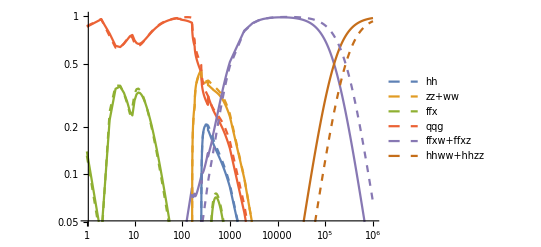

```mathematica
Show[plt4,plt5]
```

```mathematica
Life=Table[{DMMass[[i]],GeV2sec/Gammatot[[i]]},{i,1,Length[DMMass]}];
Life2=Table[{DMMass[[i]],GeV2sec/(10^-16*Gammatot[[i]])},{i,1,Length[DMMass]}];
Life3=Table[{DMMass[[i]],GeV2sec/(10^-32 Gammatot[[i]])},{i,1,Length[DMMass]}];
Cons1=Table[{DMMass[[i]],cota1},{i,1,Length[DMMass]}];
Cons2=Table[{DMMass[[i]],cota2},{i,1,Length[DMMass]}];
```

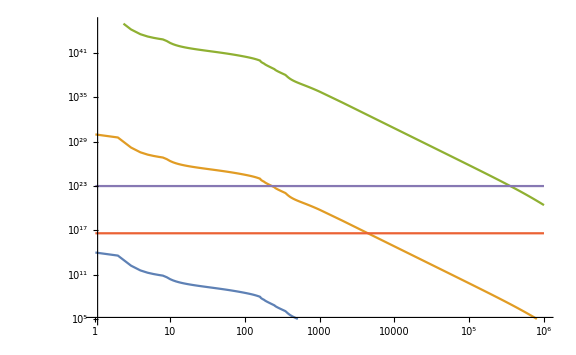

```mathematica
ListLogLogPlot[{Life,Life2,Life3,Cons1,Cons2},ImageSize->Large,Joined->True,PlotRange->{{1,10^6},{10^5,10^45}}]
```